## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.6;
```

```mathematica
winit=(0.2-0.00005*I)
```

0.2-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+10^(-3);r1=30 ;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.20187+4.98863×10^-7 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=M+10^(-3);r1=30; wc=qscal;
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-2*I*M*(wres-wc);
sigmasol=M*(qscal*wres+mu^2-2*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[
{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (wres*r^2-qscal*M*r)^2/(r-M)^4 - 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(wres-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

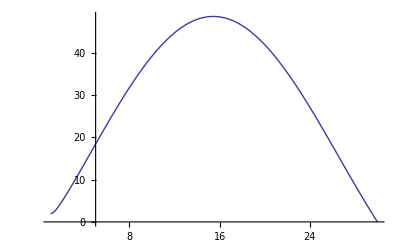

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,r0,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.2-0.00005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 +ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);

sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.2-0.00005*I);
ie=0;While[ie<51,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,50}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,50}];
```

```mathematica
winit=(0.25-0.00005*I);
ie=0;While[ie<25,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=20 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l2=Table[{N[radit[n],10],Re[witer[n]]},{n,0,24}];
t2l2=Table[{N[radit[n],10],Im[witer[n]]},{n,0,24}];
```

```mathematica
winit=(0.3-0.00005*I);
ie=0;While[ie<26,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=15 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l3=Table[{N[radit[n],10],Re[witer[n]]},{n,0,25}];
t2l3=Table[{N[radit[n],10],Im[witer[n]]},{n,0,25}];
```

```mathematica
winit=(0.45-0.00005*I);
ie=0;While[ie<16,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=10 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l4=Table[{N[radit[n],10],Re[witer[n]]},{n,0,15}];
t2l4=Table[{N[radit[n],10],Im[witer[n]]},{n,0,15}]
```

{{10.,1.57086×10^-6},{9.8,1.48283×10^-6},{9.6,1.39607×10^-6},{9.4,1.28983×10^-6},{9.2,1.18689×10^-6},{9.,1.07642×10^-6},{8.8,9.58519×10^-7},{8.6,8.35612×10^-7},{8.4,7.07573×10^-7},{8.2,5.86924×10^-7},{8.,4.61818×10^-7},{7.8,3.48312×10^-7},{7.6,2.42746×10^-7},{7.4,1.50022×10^-7},{7.2,7.64663×10^-8},{7.,2.82266×10^-8}}

```mathematica
(*The imaginary part vs the radius*)
```

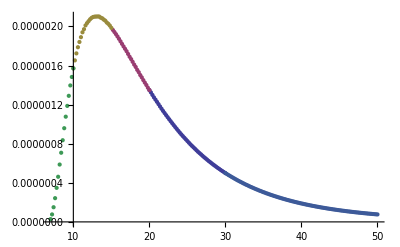

```mathematica
ListPlot[{t2l,t2l2,t2l3,t2l4,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

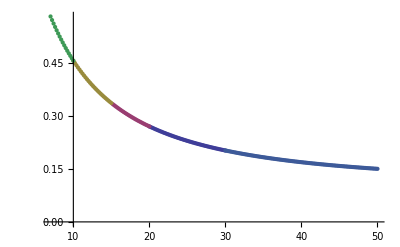

```mathematica
ListPlot[{t1l,t1l2,t1l3,t1l4,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=0.6/R.dat",Join[t1l,t1l2,t1l3,t1l4,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=0.6/I.dat",Join[t2l,t2l2,t2l3,t2l4,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=0.6/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=0.6/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-M^2]
rm=M-Sqrt[M^2-M^2]
rmirror=40
```

1

1

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*M/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.3

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```